# Lecture 14 - Capacitors

### A Puzzle...

#### Gravity Screen

Insulators are often thought of as "electrical screens," since they block out all external electric fields. For example, if neutral objects are kept inside of a conducting shell (of any shape), the electric field from any charge distribution outside the conductor will not be felt inside this cavity (by Gauss’s Law).

Example
What is wrong with the idea of a gravity screen, something that will “block” gravity the way a metal sheet seems to “block” the electric field? 
Hint: Think about the difference between the gravitational source and electrical sources.

Solution
Gravity cannot be blocked for two very important reasons:

We need opposite-signed charges to block an electric field, so we would particles with negative mass (which to date have not been discovered).

In gravitation (unlike in electricity), like charges are attracted to each other. So if we had a fixed point mass located outside a spherical shell, we could glue some negative mass on the near side of the shell in such a configuration so as to cancel the gravitational effects of this point mass inside of the shell. (We have to glue these masses, since otherwise they would be attracted towards each other and stop blocking the gravitational field.) But if this point mass was then moved, then we would need to manually update our mass configuration; this would significantly more cumbersome than the electrical case. □

#### What’s in a Candle?

Have you ever seen a candle’s flame split in two? This video demonstrates how a flame is comprised of positively and negatively charged ions, together with some dramatic repercussions that occur when you stick a flame between a parallel plate capacitor.

### Theory

#### Capacitance

The capacitance of two conductors is always calculated using the same simple recipe:

Draw your two conductors of interest in the absence of any other charges or electric fields

Give one of the conductors a charge +Q and the other a charge -Q (it does not matter which one is positive)

Calculate the (positive) voltage difference V between the two conductors

The capacitance C between two conductors is defined as

C≡Q/V

Some more notes:

We define the capacitance of a single conductor by assuming that the second conductor is a sphere with infinite radius. In other words, V is the potential difference between the surface of the conductor in the problem and infinity

Capacitance is a property of the geometry of conductors. In other words, even if in your charge configuration the two conductors have a charge Q_1 and Q_2, if you compute their capacitance you always start off by assuming that they are neutral and then assigning a charge +Q to one and -Q to the other

We will cover exactly how the charge Q gets transferred from one conductor to the other next week. As a sneak peak, you can imagine connecting a battery between the two neutral conductors which will transfer the charge Q from one to the other. We then disconnect this battery and calculate the capacitance of the resulting setup

#### Complementary Section: Two Concentric Spheres

Find the capacitance of two concentric spherical metal shells, with radii a and b.

Solution
To find the capacitance, we take Q charge from one sphere and place it on the other (it doesn’t matter which one is positive), then compute the potential difference V between the positive conductor and the negative conductor (this is positive by definition), and finally compute the capacitance

C=Q/V

For our two spheres, suppose we took Q charge from the outer sphere and transferred it to the inner sphere. The electric field between the two spheres would be

E⃗=(k Q)/r^2 r̂

so the potential difference between positively charged sphere and the negatively charged sphere would be

V=∫_a^b (k Q)/r^2 r̂=k Q (1/a-1/b)

(Note that if you end up with a negative potential, you can simply take the absolute value, as it means you computed the potential difference between the negatively charged sphere and the positively charged sphere instead of the other way around.) The capacitance is therefore

C=Q/V=1/(k (1/a-1/b))=(a b)/(k (b-a))

which is positive, as desired. □

### Problems

#### Inserting a Plate

Example 
If the capacitance in Panel (a) below is C, what is the capacitance in Panel (b), where a third plate is inserted and the outer plates are connected by a wire?

```mathematica
centerPlot@-Graphics-
```

-Graphics-

Solution
When we put charge ±Q on the two capacitors in Panel (a), it will spread out uniformly on the inner surfaces of both conductors. Since the electric field inside both conductors is zero, the Uniqueness Theorem guarantees that this is the only way the charge can be distributed.

```mathematica
centerPlot@-Graphics-
```

-Graphics-

If we define the surface charge σ=Q/A, the electric field inside will be E=σ/ϵ_0=Q/(A ϵ_0) so the potential difference between the two conductors will be V=E s=(Q s)/(A ϵ_0). Therefore C=Q/V=(A ϵ_0)/s.

Once we insert a new plate, we can use the symmetry of the problem to predict that Q/2 of charge will spread evenly on the inner surfaces of the two outer plates while -Q/2 of charge will spread evenly on both sides of the inner plate. Again, since E=0 in every conductor, and both outer conductors are at the same potential, the Uniqueness Theorem guarantees that this will be the final charge distribution.

```mathematica
centerPlot@-Graphics-
```

-Graphics-

Defining σ̃=Q/(2A), the electric field between the middle and top plate will be Ẽ=(σ̃)/ϵ_0=Q/(2A ϵ_0) so the potential difference between those two plates equals Ṽ=Ẽ s/2=(Q s)/(4A ϵ_0). Therefore C̃=Q/(Ṽ)=(4A ϵ_0)/s=4C.

In the more general case where the middle plate is a fraction f of the distance from one of the outside plates to the other, you can show that the capacitance is C/(f(1-f)). This correctly equals 4C when f=1/2. It is minimum when f=1/2 and goes to infinity as f goes to 0 or 1. □

#### Coaxial Capacitor

Example
A capacitor consists of two coaxial cylinders of length L, with inner and outer radii a and b. Assume L≫b-a, so that end corrections may be neglected. Show that the capacitance is C=(2π L ϵ_0)/Log[b/a]. Verify that if the gap between the cylinders, b-a, is very small compared with the radius, this result reduces to one that could have been obtained by using the formula for the parallel-plate capacitor.

```mathematica
{θ1,θ2}={π+π/6.,-π/3.};r2=0.4;
centerPlot@Graphics3D[{CapForm[None],Tube[{{0,0,0},{4,0,0}},1],Tube[{{0,0,0},{4,0,0}},r2],Line[{{{4,0,0},{4,Cos[θ1],Sin[θ1]}},{{4,0,0},{4,r2 Cos[θ2],r2 Sin[θ2]}}}],Text[font@"a",{4,r2/2 Cos[θ2],r2/2 Sin[θ2]}+{0.15,0,0.15}],Text[font@"b",{4,1/2 Cos[θ1],1/2 Sin[θ1]}+{0.02,0,-0.2}]},Boxed->False,ViewPoint->{2.3,-2.2,1.13},ViewVertical->{0.35,-0.12,1.87},ImageSize->200]
```

-Graphics3D-

Solutions
Assume that the inner cylinder has a charge Q while the outer cylinder has a charge -Q. Using Gauss’s Law, the electric field at a radius a<r<b is given by E⃗=Q/(2π r L ϵ_0)r̂. The (absolute value of the) potential between the two plates is given by the radial line integral going from r=a to r=b,

V=∫_a^b E⃗·ⅆ s⃗
=∫_a^b (Q/(2π r L ϵ_0)r̂)·(r̂ ⅆr)
=∫_a^b Q/(2π r L ϵ_0)ⅆr
=Q/(2π L ϵ_0)Log[b/a]

Therefore, the capacitance is given by

C=Q/V=(2π L ϵ_0)/Log[b/a]

In the limit of a small gap s=b-a≪a, we can Taylor expand the logarithm as

Log[b/a]=Log[(a+s)/a]=Log[1+s/a]≈s/a+O[s/a]^2

Noting that the area of either cylinder in this limit equals A=2π a L, the capacitance reduces to

C=(2π L ϵ_0)/(s/a)=(A ϵ_0)/s

which is identical to the capacitance of parallel plates. This must be the case, since in the limit s≪a, we can think of the two cylinders as many parallel plate capacitors connected in parallel (see Problem 3.18). □

#### Capacitor Paradox

Example 
Two capacitors with the same capacitance C and charge Q are placed next to each other. The two positive plates are then connected by a wire. Will charge ﬂow in the wire? Consider two possible scenarios:

```mathematica
centerPlot@-Graphics-
```

-Graphics-

(A) Before the plates are connected, the potential differences of the two capacitors are the same (because Q and C are the same). So the potentials of the two positive plates are equal. Therefore, no charge will ﬂow in the wire when the plates are connected.

(B) Number the plates 1 through 4, from left to right. Before the plates are connected, there is zero electric field in the region between the capacitors, so plate 3 must be at the same potential as plate 2. But plate 2 is at a lower potential than plate 1. Therefore, plate 3 is at a lower potential than plate 1, so charge will ﬂow in the wire when the plates are connected.

Which reasoning is correct, and what is wrong with the wrong reasoning?

Solution
Reasoning (B) is correct. Plate 3 is indeed at a lower potential than plate 1, so charge will flow. The error in the first reasoning is encompassed in the word, "So." Although it is true that the potential differences of the two capacitors are the same, this does not imply that the potentials of the two positive plates are equal. If we arbitrarily assign zero potential to plate 1, and if the common potential difference is ϕ, then the potentials of the fours plates are, from left to right, 0, -ϕ, -ϕ, -2ϕ. No matter where we define the zero of potential, the potential of the leftmost plate is ϕ larger than the potential of the third plate, and 2ϕ larger than the potential of the rightmost plate. □

#### A Four-Plate Capacitor

Example
Consider a capacitor made of four parallel plates with large area A, evenly spaced with small separation s. The first and third are connected by a wire, as are the second and fourth. What is the capacitance of this system?

```mathematica
x=0.2;dx=0.2;r=0.4;
centerPlot@Graphics[{Line[{{{-x,0},{-x,1}},{{x,0},{x,1}},{{-x+dx,0},{-x+dx,1}},{{x+dx,0},{x+dx,1}}}],Dashed,Circle[{0,√(r^2-x^2)-0.01},r,{3π/2-ArcTan[x/r],3π/2+ArcTan[x/r]}],Circle[{dx,1-√(r^2-x^2)+0.01},r,{π/2-ArcTan[x/r],π/2+ArcTan[x/r]}],Text["Wire",{0,-0.15}],Text["Wire",{dx,1.14}]},ImageSize->100]
```

-Graphics-

Solution
Assume that the left-most sheet (and the sheet that it is connected to) have a charge Q, while the remaining two connected sheets have a charge -Q. First, note the symmetry of the system - reflecting about the plane between the middle two sheets and switching the signs of all charges reproduces an identical system. The charge distributions on the sheets must obey this same symmetry, so let us label them as

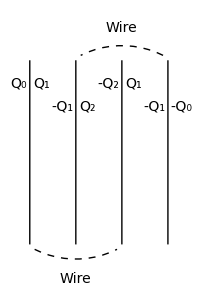

```mathematica
x=0.2;dx=0.2;r=0.4;s=0.06;s2=0.05;{b,h}={0.2,1};
centerPlot@Graphics[{Line[{{{-x,b},{-x,h}},{{x,b},{x,h}},{{-x+dx,b},{-x+dx,h}},{{x+dx,b},{x+dx,h}}}],Dashed,Circle[{0,b+√(r^2-x^2)-0.01},r,{3π/2-ArcTan[x/r],3π/2+ArcTan[x/r]}],Circle[{dx,h-√(r^2-x^2)+0.01},r,{π/2-ArcTan[x/r],π/2+ArcTan[x/r]}],Text[font@"Wire",{0,b-0.15}],Text[font@"Wire",{dx,1.14}],Text[font@"Q_0",{-x-s2,0.9}],Text[font@"Q_1",{-x+s2,0.9}],Text[font@"-Q_1",{-s,0.8}],Text[font@"Q_2",{s2,0.8}],Text[font@"-Q_2",{x-s,0.9}],Text[font@"Q_1",{x+s2,0.9}],Text[font@"-Q_1",{2x-s,0.8}],Text[font@"-Q_0",{2x+s,0.8}]},ImageSize->200]
```

There are several things to note about this setup:

The charges Q_j above represent charge distributed uniformly across each surface. This must be the case because we are ignoring edge effects and we know that the electric field must be perpendicular to the surface of a conductor, so this is the most general charge configuration that is possible

Why do the charges on the two left-most surfaces have to be Q_1 and -Q_1? Consider a Gaussian pillbox (shown in blue below) that spans this space and whose faces lie inside these two conductors. The electric field inside the conductors equals zero, and the field between the conductors points perpendicular to the sheets, so that ∮E⃗·ⅆ a⃗=0=q_enc/ϵ_0. Thus the charge densities on the two adjacent surfaces must be equal and opposite.

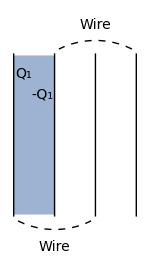

```mathematica
x=0.2;dx=0.2;r=0.4;s=0.06;s2=0.05;{b,h}={0.2,1};
centerPlot@Graphics[{{color1,Opacity[0.6],Rectangle[{-x,b+0.01},{0,h-0.01}]},Line[{{{-x,b},{-x,h}},{{x,b},{x,h}},{{-x+dx,b},{-x+dx,h}},{{x+dx,b},{x+dx,h}}}],Dashed,Circle[{0,b+√(r^2-x^2)-0.01},r,{3π/2-ArcTan[x/r],3π/2+ArcTan[x/r]}],Circle[{dx,h-√(r^2-x^2)+0.01},r,{π/2-ArcTan[x/r],π/2+ArcTan[x/r]}],Text[font@"Wire",{0,b-0.15}],Text[font@"Wire",{dx,1.14}],Text[font@"Q_1",{-x+s2,0.9}],Text[font@"-Q_1",{-s,0.8}]},ImageSize->150]
```

By this same reasoning, the charge densities on the facing surfaces of the two middle plates must be Q_2 and -Q_2

The charge densities on the facing surfaces of the two right-most plates are Q_1 and -Q_1 using the charge conjugation + reflection symmetry discussed above. Similarly, the charge on the two outer-most surfaces must be Q_0 and -Q_0 by these same symmetries.

The charge Q_0=0 in order for there to be no electric field inside of the conducting sheets

The total charges on the plates are constrained by the fact that the left-most sheet has charge Q while the right-most sheet has charge -Q,

2 Q_1-Q_2=Q

The potential difference between the two left-most sheets is (Q_1 s)/(A ϵ_0), with the left-most sheet having the higher potential if Q_1>0. Similarly, the potential difference between the two middle sheets is (Q_2 s)/(A ϵ_0), with the left sheet in the pair having the higher potential if Q_2>0. Since the left-most sheet and the middle-right sheet must be at the same potential (since they are connected by a wire), we must have Q_2=-Q_1. Substituting this into Equation (TextNumbered), we find Q_1=Q_3, so that the full configuration looks as follows:

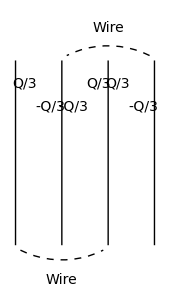

```mathematica
x=0.2;dx=0.2;r=0.4;s=0.05;s2=0.04;{b,h}={0.2,1};
centerPlot@Graphics[{Line[{{{-x,b},{-x,h}},{{x,b},{x,h}},{{-x+dx,b},{-x+dx,h}},{{x+dx,b},{x+dx,h}}}],Dashed,Circle[{0,b+√(r^2-x^2)-0.01},r,{3π/2-ArcTan[x/r],3π/2+ArcTan[x/r]}],Circle[{dx,h-√(r^2-x^2)+0.01},r,{π/2-ArcTan[x/r],π/2+ArcTan[x/r]}],Text[font@"Wire",{0,b-0.15}],Text[font@"Wire",{dx,1.14}],Text[font@"Q/3",{-x+s2,0.9}],Text[font@"-Q/3",{-s,0.8}],Text[font@"-Q/3",{s,0.8}],Text[font@"Q/3",{x-s2,0.9}],Text[font@"Q/3",{x+s2,0.9}],Text[font@"-Q/3",{2x-s,0.8}]},ImageSize->170]
```

The potential difference between the two conductors in this system equals V=(Q s)/(3A ϵ_0), so that the capacitance is given by

C=Q/V=(3A ϵ_0)/s

as desired. □

#### A 2N-Plate Capacitor

Example
Consider the setup in the previous problem, but now with 2N parallel plates instead of four. The first, third, fifth, etc. plates are connected by wires, and likewise for the second, fourth, sixth, etc. plates. What is the capacitance of this system? What does it equal in the N→∞ limit?

Solution
From the above problem, a clear pattern emerges for 2N parallel plates: Plates will alternative between being positively charged and negatively charged, and every surface (except for the two outer-most surfaces) will have charge Q/(2N-1). Therefore, the potential difference between the two conductors will be V=(Q s)/((2N-1)A ϵ_0) and the capacitance will equal

C=Q/V=((2N-1)A ϵ_0)/s

In the limit N→∞, the capacitance approaches C≈(2N A ϵ_0)/s, which is larger than the capacitance we would have obtained if we had simply juxtaposed the two pairs of N plates to create two plates with an area N A each. If we keep the separation s, then the capacitance of the resulting standard two-plate capacitor would be C=(N A ϵ_0)/s. The reason why this capacitance is larger is that we effectively have 2N-1 identical area capacitors of alternating orientation lined up next to each other, instead of N capacitors with the same orientation. □

#### A Three-Shell Capacitor

Example
A capacitor consists of three concentric spherical shells with radii R, 2R, and 3R. The inner and outer shells are connected by a wire (passing through a hole in the middle shell, without touching it), so they are at the same potential. The shells start neutral, and then a battery transfers charge from the middle shell to the inner and outer shells. 
1. If the final charge on the middle shell is −Q, what are the charges on the inner and outer shells? 
2. What is the capacitance of the system? 
3. If the battery is disconnected, what happens to the three charges on the shells if charge q is added to the outer shell?

Solution
1. Because of the spherical symmetry, all charges will be spread uniformly across each surface.

Method 1: Let Q_1 be the final charge on the outside surface of the inner sphere. Let Q_3 be the final charge on the inside surface of the outer sphere. (There cannot be any charge on the inside surface of inner sphere, since that would make a non-zero field inside the meat of the inner sphere. Similarly, a Gaussian sphere surface inside of the outer sphere show that there must be zero net charge inside of this surface, which implies that Q_1+Q_3=+Q. Because the conductors are neutral, there is no charge leftover to be on the outer surface of the outer sphere.)

The electric field between the inner sphere and the middle sphere will be due solely to the charge Q_1 on the inner sphere, (k Q_1)/r^2 r̂. Hence, the potential difference between the middle and inner spheres will be

k Q_1(1/R-1/(2R))

where the middle sphere has the lower potential. The electric field between the middle and outer spheres will be ((k Q_1)/r^2-(k Q)/r^2)r̂ (which will point inwards), so the potential difference between the outer and middle spheres will be

k (Q_1-Q)(1/(2R)-1/(3R))

with the middle shell at lower potential. Because the inner and outer shells must be at the same potential,

k Q_1(1/R-1/(2R))+k (Q_1-Q)(1/(2R)-1/(3R))=0

which yields Q_1=Q/4. As stated above, Q_1+Q_3=+Q so that Q_3=(3Q)/4.

Method 2: To really nail this problem, we could compute the charge density on every surface of every spherical conductor. Gauss’s Law on the inner sphere tells us that there can be no charge on the inner surface of the inner sphere. So let’s label the remaining surface charge densities σ_1,σ_2,σ_3,σ_4,and σ_5 from inside to outside as shown below.

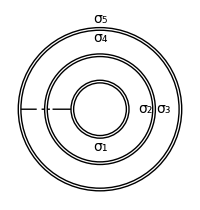

```mathematica
r2=0.1;r3=0.25;r4=0.07;ft=Style[#,14]&;θ1=-π/2;θ2=0;θ3=π/2;
centerPlot@Graphics[{Circle[{0,0},#]&/@{1,2,3,1+r2,2+r2,3+r2},Text[ft@"σ_1",(1+r2+r3+r4){Cos[θ1],Sin[θ1]}],Text[ft@"σ_2",(2-r2-r3+r4){Cos[θ2],Sin[θ2]}],Text[ft@"σ_3",(2+r2+r3+r4){Cos[θ2],Sin[θ2]}],Text[ft@"σ_4",(3-r2-r3+r4){Cos[θ3],Sin[θ3]}],Text[ft@"σ_5",(3+r2+r3+r4){Cos[θ3],Sin[θ3]}],Line[{{-1-r2,0},{-2+0.2,0}}],Line[{{-2-0.4,0},{-3,0}}],Dashing[Tiny],Line[{{-2+0.1,0},{-2-0.3,0}}]},ImageSize->200]
```

What constraints do we have on the system? First, the total charge on the inner and outer spheres must be +Q.

4π (R^2 σ_1+(3R)^2(σ_4+σ_5))=Q

Additionally, the total charge on the middle sphere must be -Q

4π ((2R)^2(σ_2+σ_3))=-Q

Using Gauss’s Law (inside of the middle conductor), the total charge from the σ_1 surface must cancel the charge from the σ_2 surface, and similarly (for a Gaussian surface inside of the outer conductor) the total charge from the σ_1,σ_2,σ_3,and σ_4 surfaces must sum to zero,

4π (R^2 σ_1+(2R)^2 σ_2)=0

4π (R^2 σ_1+(2R)^2(σ_2+σ_3)+(3R)^2 σ_4)=0

Lastly, we know that the potential on the inner sphere and the outer sphere must be the same. The potential difference between the inner and middle spheres equals ∫_R^(2R) (k (4π R^2 σ_1))/r^2 ⅆr=2 k π R σ_1 while the potential difference between the middle and outer spheres equals ∫_(2R)^(3R) (k (4π R^2 σ_1+4π (2R)^2(σ_2+σ_3)))/r^2 ⅆr=2/3 k π R (σ_1+4 (σ_2+σ_3)). The sum of these two must be zero,

2 k π R σ_1+2/3 k π R (σ_1+4 (σ_2+σ_3))=0

Solving equations (TextNumbered)-(TextNumbered) yields

σ_1=Q/(16π R^2)

σ_2=-Q/(16π (2R)^2)

σ_3=(-3Q)/(16π (2R)^2)

σ_4=(3Q)/(16π (3R)^2)

σ_5=0

```mathematica
sol=Solve[{4π(2R)^2(σ2+σ3)==-Q,4π(R)^2(σ1)+4π(3R)^2(σ4+σ5)==Q,4π(R^2 σ1+(2R)^2 σ2)==0,4π(R^2 σ1+(2R)^2(σ2+σ3)+(3R)^2 σ4)==0,0==2 k π R σ1+2/3 k π R (σ1+4 (σ2+σ3))},{σ1,σ2,σ3,σ4,σ5}]
```

{{σ1→Q/(16 π R^2),σ2→-Q/(64 π R^2),σ3→-(3 Q)/(64 π R^2),σ4→Q/(48 π R^2),σ5→0}}

We could have predicted that σ_5=0 by noting that a spherical Gaussian surface inside of the outer sphere shows that there must be zero net charge inside of this surface, which implies that a total of +Q charge must reside on the σ_1 and σ_4 surfaces; because the conductors are neutral, there is no charge leftover for the σ_5 surface.

2. As we found above, the potential difference between the inner and middle spherical shells equals

V=k Q_1(1/R-1/(2R))=k Q/4(1/(2R))=(k Q)/(8R)

Therefore, the capacitance equals

C=Q/V=(8R)/k=32π ϵ_0 R

3. One obvious solution is that the charge q simply distributes itself over the outer surface of the outside sphere (called σ_5 in Method 2 above). This charge distribution would still keep the electric field inside every conductor zero, and the potential difference between the inner and outer spheres would remain the same. Thus, by the Uniqueness Theorem, this is indeed the final charge configuration. So the charges on the inner and middle spheres will not change at all, and the charge on the inner surface of the outside sphere will not change, but the charge q will distribute itself uniformly over the outer surface of the outside sphere. □

#### Advanced Section: Edge Effects

Let us return to the canonical example of a parallel plate capacitor. As discussed in Equation (3.13), the total charge on the top plate of this capacitor is given by

Q=A (ϵ_0(ϕ_1-ϕ_2))/s     (neglecting edge effects)

```mathematica
centerPlot@-Graphics-
```

-Graphics-

From this point on, it is important to keep in the back of your mind that our dealings with the parallel plate capacitor will almost always involve neglecting edge effects. This "almost" is especially important because we will occasionally look at phenomena that are entirely caused by edge effects. At such points, it is sometimes difficult to separate out what we have learned that is hinges on neglecting edge effects and what is generally true. As a simple example, consider the potential difference between the middle points on the top and bottom conductors shown above.

```mathematica
centerPlot@-Graphics-
```

-Graphics-

Far away from the edges, the electric field inside the capacitor will be uniform, so that the potential difference along any path from A to B (including the straight line path between them) must equal σ/ϵ_0 s. So what about an exterior path between A and B? If we neglect edge effects, then the electric field outside the capacitor is zero, and so we would incorrectly conclude that the potential difference between A and B is 0. But we know one of these results must be wrong, since the potential between any two points is independent of the path taken between these two points, and indeed it is this latter argument (which neglects edge effects) which is incorrect.

Another interesting example is considered in "Advanced Section: Conductor in a Capacitor" below, where we discuss how a conducting slab is sucked into a parallel plate capacitor entirely due to edge effects.

#### Advanced Section: Conductor in a Capacitor

Example  
1. The plates of a capacitor have area A and separation s (assumed to be small). The plates are isolated, so the charges on them remain constant; the charge densities are ±σ. A neutral conducting slab with the same area A but thickness s/2 is initially held outside the capacitor. The slab is released. What is its kinetic energy at the moment it is completely inside the capacitor? (The slab will indeed get drawn into the capacitor, as evidenced by the fact that the kinetic energy you calculate will be positive.)

```mathematica
centerPlot@-Graphics-
```

-Graphics-

2. Same question, but now let the plates be connected to a battery that maintains a constant potential difference. The charge densities are initially ±σ. (Don’t forget to include the work done by the battery, which you will find to be nonzero.)

Some Comments
This problem deserves several remarks before we tackle it head on. The most pressing issue is why should there be any force sucking in the conductor at all. The answer lies in the fringe fields of the parallel plate capacitor inducing a non-uniform charge density σ in the conductor. Consider the picture below (which has the conductor spanning the entire width of the parallel plates for simplicity, but the same reasoning will hold nonetheless in the current problem).

```mathematica
centerPlot@-Graphics-
```

-Graphics-

As discussed within the section "Advanced Section: Electrostatic Pressure" in Lecture 12, any patch on a conductor’s surface with charge density σ feels an outwards pressure of σ^2/(2 ϵ_0). On the top and bottom surfaces of the conductor, these two pressures are equal and opposite, but the pressure on the right surface of the conductor will be much larger than the pressure on the left face of the conductor, and consequently this conductor will get sucked into the parallel plates.

Lastly, we note that after the conductor gets sucked into the capacitor, its nonzero kinetic energy will drive it onward through the capacitor. The resulting motion will be an oscillation with the conductor just barely exiting the capacitor on either side.

We now determine exactly how much kinetic energy the conductor will have when it is fully embedded int he capacitor.

Solution
1. The initial energy U_i of the system is ϵ_0/2 E^2 times the volume A s between the capacitors. Using E=σ/ϵ_0,

U_i=(σ^2 A s)/(2 ϵ_0)

When the conducting slab is completely inside the capacitor, a surface charge -σ will accrue on the top of the slab and a surface charge +σ will accrue on the bottom of the slab, in order to cancel out the electric field everywhere inside the conducting slab.

```mathematica
centerPlot@-Graphics-
```

-Graphics-

The electric field above the slab will still be E=σ/ϵ_0 as before, so the total energy U_f in the new system will be ϵ_0/2 E^2 times the volume (A s)/2 between the capacitors,

U_f=(σ^2 A s)/(4 ϵ_0)

The kinetic energy will be the difference in the two energies of the system,

K=U_i-U_f=(σ^2 A s)/(4 ϵ_0)

2. As in the first part of this problem, initially U_i=(σ^2 A s)/(2 ϵ_0). Once the slab is inside of the capacitor, there will be charge densities σ' and -σ' on the various surfaces as shown below.

```mathematica
centerPlot@-Graphics-
```

-Graphics-

The potential difference between the two plates equals (E s)/2=(σ' s)/(2 ϵ_0). The battery maintains a constant potential difference, which was (σ s)/ϵ_0 initially. Therefore σ'=2σ and the final energy stored in the capacitors equals

U_f=ϵ_0/2 E^2(A s)/2
=ϵ_0/2(σ'/ϵ_0)^2(A s)/2
=ϵ_0/2((2σ)/ϵ_0)^2(A s)/2
=(σ^2 A s)/ϵ_0

If there weren’t anything else going on, this would violate energy conservation, since the system ends up with more energy than it started out. However, the battery must do work to maintain a constant potential difference between the two plates. It does this by transferring charge from the negative plate to the positive plate. In total, the battery moves σ A of charge across the constant potential difference (σ s)/ϵ_0, so the total work it performs equals

W=(σ^2 A s)/ϵ_0

We can now apply conservation of energy to find the kinetic energy K of the slab,

W+U_i=U_f+K

which yields

K=(σ^2 A s)/(2 ϵ_0)

Basically, of the (σ^2 A s)/ϵ_0 work done by the battery, half goes into increasing U_i, and half goes into K. It makes sense that the K here is larger than the K in the first part of this problem, because  with more charge on the plates, so the forces involved are larger. □

## Mathematica Initialization

```mathematica
Clear[font]
font[text_,size_Integer:14,opts___]:=(Style[text,size,FontFamily->"Times",opts])
```

```mathematica
RawBoxes@CounterBox["TextNumbered","eq1"]
```

TextNumbered

```mathematica
{color1,color2,color3}=ColorData[97][#]&/@{1,10,6};
```